Last modified on: Thursday, July 12, 2018 at 6:02

Author Info

Rishab Nayak

Garrett Ducharme

Boston University

Poster Session Content

A Performance Analysis of Neural Networks to Identify Plugs and Connectors from an Image

Analyze the performance of different Neural Networks to solve the same problem: Identify plugs and connectors from its image. This would allow us to understand the implications of using different network frameworks on accuracy and compute time, and understand the tradeoffs.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics--Graphics-

On analyzing the data, it was found that the Ademxapp v2 network performed the best, with an accuracy of 91%, but also was one of the slowest networks, having an evaluation time of 1.10s. The fastest network was the ImageIdentify v2 network, with an evaluation time of 0.062s, however, it compromised on accuracy, dropping to 82%. 
From the data collected, it appears that there exists a direct relationship between accuracy and speed for Neural Networks. As the depth of the network increases, the accuracy increases, corresponding to an increase in evaluation time.

Use a more diverse dataset, recognize more categories of images.
Implement a faster version of the network/networks as an API for use as an app for mobile phones, part of a larger application that provides users with contextual awareness about their environment.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Best Performer: Accuracy

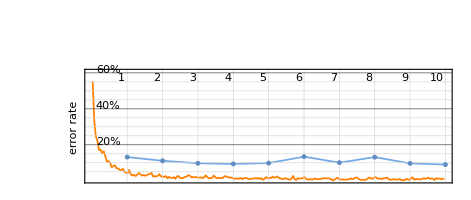
The Ademxapp v2 Net trained on a dataset containing a total of 24000 images of 32 Port and connector categories was 91% accurate at classifying input images. This network is a high performance model which aimed to find a proper depth for ResNets, improving on the feature search method, trying to classify images accurately without grid-searching the whole space. As a result, the original network had only 17 residual units, and outperformed various deeper architectures. 

Modifying the Network, I added an ImageAugmentation Layer to augment the dataset, producing reflected versions of the input images along both the x and y axes, with a probability of 0.5 for both. The residual units 6a and 7a were allowed to retrain, along with the Batch Normalization Layer bn7, and the penultimate Linear Layer, which was followed up with a Softmax Layer. The final NetChain was - 
-Graphics-
The error rate fell quite fast during the first few training rounds, and then plateaued. The validation error fluctuated in tandem with the training error, a good sign, showing that the network was stable.
-Graphics-

Best Performer: Evaluation Time

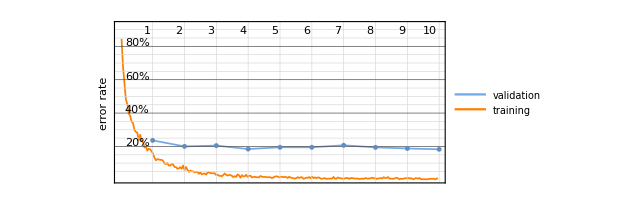
The ImageIdentify v2 network, again was trained on the same dataset used to train the Ademxapp v2 network. This network is based off of Wolfram’s Image Identify Network, and uses transfer learning to speed up the training process.  This network was the fastest in terms of runtime, but suffered in terms of accuracy. The network was right only 82% of the time, but evaluated in merely 0.062s. It also had a much smaller memory footprint, weighing in at 42MB. 

This network was modified similarly to the Ademxapp v2 network to augment images, and the NetGraph Layer 5b was allowed to retrain. The network architecture was - 
-Graphics-
This network converged satisfactorily too, however, the gap between the validation and training error evolutions were more noticeable, suggesting that the network wasn’t as great at recognizing patterns as Ademxapp v2.
-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

I trained 10 Neural Networks in total, and calculated their evaluation times and accuracies. Most of the networks behaved as expected, however, there were a few anomalies. For example, VGG-19 v2 never trained, and the accuracy thus didn’t cross 4%. 

The Ademxapp v2 network was the most accurate network, measuring in at 91%, but was also the slowest, taking 1.10s to evaluate. This network is a high performance model which aimed to find a proper depth for ResNets, improving on the feature search method, trying to classify images accurately without grid-searching the whole space. As a result, the original network had only 17 residual units, and outperformed various deeper architectures. 

The ImageIdentify v2 network was the fastest network, evaluating in merely 0.062s, and weighing in at 42MB. It also had an accuracy of 82%. This network was based off of Wolfram’s Image Identify Network, and uses transfer learning to speed up the training process.

#### Code

##### Data Preparation

Enumerate Recognizable Entities

```mathematica
entityList={"MIDImale","MIDIfemale","RJ45male","RJ45female","TOSLINKmale","TOSLINKfemale","compositevideomalecable","compositevideoport","componentvideocable","componentvideoport","VGAcable","VGAport","dvicable","dviport","minidisplayportcable","minidisplayportport","HDMIcable","HDMIport","DisplayPortcable","DisplayPortport","usbamale","usbafemale","usbcmale","usbcfemale","microusbfemale","microusbmalecable","firewire800cable","firewire800port","firewire400port","firewire400cable","coaxcable","coaxport"};
```

Import Random Backgrounds to use as Underlay

```mathematica
allbackgrounds = Import[StringJoin[NotebookDirectory[],"Backgrounds/",ToString@#,".jpg"]]&/@Range[868];
```

```mathematica
backgrounds = ImageResize[#,{700,700}]&/@allbackgrounds;
```

Process All Images (Resize, Rotate, and use ImageCompose) to Create the Training and Validation Dataset

```mathematica
processAllTraining[foldername_,backgrounds_]:=Block[{inputimages,croppedimages,rotated1,rotated2,rotated3,rotated4, rotated5,rotated6,rotated7,rotated8,rotated9,rotated10,rotated11,rotated12,rotated13,rotated14,rotated15,rotated16,rotatedimages,overlaid,resized,images},
inputimages=Import[StringJoin[NotebookDirectory[],"Images/",foldername,"/",ToString@#,".png"]]&/@Range[50];
croppedimages = ImageCrop[#]&/@inputimages;
images=ImageResize[#,{320,320}]&/@croppedimages;
rotated1=ImageRotate[#,5 Degree]&/@images;
rotated2=ImageRotate[#,-5 Degree]&/@images;
rotated3=ImageRotate[#,10 Degree]&/@images;
rotated4=ImageRotate[#,-10 Degree]&/@images;
rotated5=ImageRotate[#,15 Degree]&/@images;
rotated6=ImageRotate[#,-15 Degree]&/@images;
rotated7=ImageRotate[#,20 Degree]&/@images;
rotated8=ImageRotate[#,-20 Degree]&/@images;
rotated9=ImageRotate[#,25 Degree]&/@images;rotated10=ImageRotate[#,-25 Degree]&/@images;
rotated11=ImageRotate[#,30 Degree]&/@images;rotated12=ImageRotate[#,-30 Degree]&/@images;rotated13=ImageRotate[#,35 Degree]&/@images;rotated14=ImageRotate[#,-35 Degree]&/@images;rotated15=ImageRotate[#,40 Degree]&/@images;rotated16=ImageRotate[#,-40 Degree]&/@images;
rotatedimages = Join[rotated1,rotated2,rotated3,rotated4, rotated5,rotated6,rotated7,rotated8,rotated9,rotated10,rotated11,rotated12,rotated13,rotated14,rotated15,rotated16];
overlaid = ImageCompose[RandomSample[backgrounds,1][[1]],RemoveBackground@#,{{160,160}},{Center,Center}]&/@rotatedimages;
resized = ImageResize[#,{320,320}]&/@overlaid;
Export[StringJoin[NotebookDirectory[],"Images/",foldername,".mx"],#&/@resized];
Print[foldername];
];
```

```mathematica
processAllTraining[#,backgrounds]&/@entityList;
```

Validation Set is Independent of the Training Set to Improve Accuracy

```mathematica
processAllValidation[foldername_,backgrounds_]:=Block[{inputimages,croppedimages,overlaid,resized,images,validation},
inputimages=Import[StringJoin[NotebookDirectory[],"Images/",foldername,"/",ToString@#,".png"]]&/@Range[50];
croppedimages = ImageCrop[#]&/@inputimages;
images=ImageResize[#,{320,320}]&/@croppedimages;
overlaid = ImageCompose[RandomSample[backgrounds,1][[1]],RemoveBackground@#,{{160,160}},{Center,Center}]&/@images;
resized = ImageResize[#,{320,320}]&/@overlaid;
validation = Join[resized,images];
Export[StringJoin[NotebookDirectory[],"Images/",foldername,"validation",".mx"],#&/@validation];
Print[foldername];
];
```

```mathematica
processAllValidation[#,backgrounds]&/@entityList;
```

Convert List of Images to List of Replacement Rules - Create Database

```mathematica
saveRuleListTraining[foldername_]:=Block[{images},
images=Import[StringJoin[NotebookDirectory[],"Images/",foldername,".mx"]];
Export[StringJoin[NotebookDirectory[],"Images/",foldername,".mx"],Thread[#->foldername]&/@images
];
];
```

```mathematica
saveRuleListTraining[#]&/@entityList;
```

```mathematica
saveRuleListValidation[foldername_]:=Block[{images},
images=Import[StringJoin[NotebookDirectory[],"Images/",foldername,"validation",".mx"]];
Export[StringJoin[NotebookDirectory[],"Images/",foldername,"validation",".mx"],Thread[#->foldername]&/@images
];
];
```

```mathematica
saveRuleListValidation[#]&/@entityList;
```

Join Individual Lists of Replacement Rules to Create a List of All Rules

```mathematica
finalRules[]:=Block[{ruleList,validationrulelist},ruleList=Flatten[Join[Import[FileNames[StringJoin[NotebookDirectory[],"Images/",#,".mx"]][[1]]]&/@entityList]];
validationrulelist = Flatten[Join[Import[FileNames[StringJoin[NotebookDirectory[],"Images/",#,"validation",".mx"]][[1]]]&/@entityList]];
Export[StringJoin[NotebookDirectory[],"Test.mx"],ruleList];
Export[StringJoin[NotebookDirectory[],"Validation.mx"],validationrulelist];
];
```

```mathematica
finalRules[];
```

Randomize Arrangement of Replacement Rules to Ensure Batches Have All Types of Data

```mathematica
trainingset=RandomSample[trainingrules,All];
validationset=RandomSample[validationrules,All];
```

##### Image Classification

Attempt 1: Classifier

```mathematica
classifier = Classify[trainingset,ValidationSet->validationset,PerformanceGoal->"Quality"];
```

```mathematica
ClassifierInformation[classifier]
```

Classifier information
Input type | Image
Number of classes | 32
Method | LogisticRegression
Accuracy | 65.9 % ± 4. %
Loss | 1.18 ± 0.11
Single evaluation time | 91. ms/example
Batch evaluation speed | 11.1 examples/s
Classifier memory | 3.9 MB
Training examples used | 1280 examples
Training time | 2 56
 |

Attempt 2: Neural Networks v1

These Neural Networks were trained using Transfer Learning, using the first few layers of an original, trained network, leaving them unchanged and frozen, adding an ImageAugmentation Layer at the beginning of the Network to produce reflected versions of the input images along both the x and y axes, with a probability of 0.5 for both. The networks were cut off before the final Linear Layer, and a new Linear Layer was added to reflect the different output dimensions, which was followed up with a Softmax Layer to create a final one-hot vector for the output. The Output Decoder was setup to recognize classes, the classes being the names of the recognizable entities. The networks used to extracted the pretrained networks were:

Ademxapp Model A

Inception V3

ResNet-152

VGG-19

ImageIdentify

Attempt 3: Neural Networks v2

These Neural Networks were yet again trained using Transfer Learning, similar to v1 Networks, adding an ImageAugmentation Layer at the beginning, and a Linear Layer followed by a Softmax Layer at the end of the network. What was different was that that the entire network wasn’t frozen, the last few layers of each of these networks were retrained, which boosted up the accuracy significantly.

##### Neural Networks

ImageIdentify v1

```mathematica
imageidentifyNet=Take[NetModel["Wolfram ImageIdentify Net for WL 11.1"],{1,-3}];
myimageidentifynet=NetChain[Association["auglayer"->ImageAugmentationLayer[{224,224},"ReflectionProbabilities"->{0.5,0.5}],"pretrainednet"->imageidentifyNet,"linear"->LinearLayer[],"softmax"->SoftmaxLayer[]],"Input"->NetEncoder[{"Image",{224,224},"MeanImage"->{0.48,0.46,0.4}}],"Output"->NetDecoder[{"Class",connList}]];
trainedimageidentifyNet=NetTrain[myimageidentifynet,trainingset,All,BatchSize->32,LearningRateMultipliers->{"linear"->1,_->0},ValidationSet->validationset,TargetDevice->"GPU",TrainingProgressCheckpointing->{"File","checkpointimageidentifynet.wlnet"}];
Export["trainedimageidentifyNet.wlnet",trainedimageidentifyNet["TrainedNet"]];
Export["trainedimageidentifyNet.mx",trainedimageidentifyNet];
```

Ademxapp v1

```mathematica
ademNet=Take[NetModel["Ademxapp Model A Trained on ImageNet Competition Data"],{1,-3}];
myademnet=NetChain[Association["augLayer"->ImageAugmentationLayer[{320,320},"ReflectionProbabilities"->{0.5,0.5}],"pretrainednet"->ademNet,"linear"->LinearLayer[],"softmax"->SoftmaxLayer[]],"Input"->NetEncoder[{"Image",{320,320},"MeanImage"->{0.485,0.456,0.406},"VarianceImage"->{0.0524,0.0502,0.0506}}],"Output"->NetDecoder[{"Class",connList}]];
trainedademNet=NetTrain[myademnet,trainingset,All,BatchSize->32,LearningRateMultipliers->{"linear"->1,_->0},ValidationSet->validationset,TargetDevice->"GPU",TrainingProgressCheckpointing->{"File","checkpointademnet.wlnet"}];
Export["trainedademNet.wlnet",trainedademNet["TrainedNet"]];
Export["trainedademNet.mx",trainedademNet];
```

Inception v1

```mathematica
inceptionNet=Take[NetModel["Inception V3 Trained on ImageNet Competition Data"],{1,-4}];
myinceptionnet=NetChain[Association["augLayer"->ImageAugmentationLayer[{299,299},"ReflectionProbabilities"->{0.5,0.5}],"pretrainednet"->inceptionNet,"linear"->LinearLayer[],"softmax"->SoftmaxLayer[]],"Input"->NetEncoder[{"Image",{299,299},"MeanImage"->{0.5,0.5,0.5}}],"Output"->NetDecoder[{"Class",connList}]];
trainedinceptionNet=NetTrain[myinceptionnet,trainingset,All,BatchSize->32,LearningRateMultipliers->{"linear"->1,_->0},ValidationSet->validationset,TargetDevice->"GPU",TrainingProgressCheckpointing->{"File","checkpointinceptionnet.wlnet"}];
Export["trainedinceptionNet.wlnet",trainedinceptionNet["TrainedNet"]];
Export["trainedinceptionNet.mx",trainedinceptionNet];
```

VGG-19 v1

```mathematica
vgg19Net=Take[NetModel["VGG-19 Trained on ImageNet Competition Data"],{1,-9}];
myvgg19net=NetChain[Association["augLayer"->ImageAugmentationLayer[{224,224},"ReflectionProbabilities"->{0.5,0.5}],"pretrainednet"->vgg19Net,"linear"->LinearLayer[],"softmax"->SoftmaxLayer[]],"Input"->NetEncoder[{"Image",{224,224},"MeanImage"->{0.4850196078431373,0.457956862745098,0.4076039215686274}}],"Output"->NetDecoder[{"Class",connList}]];
trainedvgg19Net=NetTrain[myvgg19net,trainingset,All,BatchSize->32,LearningRateMultipliers->{"linear"->1,_->0},ValidationSet->validationset,TargetDevice->"GPU",TrainingProgressCheckpointing->{"File","checkpointvgg19net.wlnet"}];
Export["trainedvgg19Net.wlnet",trainedvgg19Net["TrainedNet"]];
Export["trainedvgg19Net.mx",trainedvgg19Net];
```

ResNet-152 v1

```mathematica
resNet=Take[NetModel["ResNet-152 Trained on ImageNet Competition Data"],{1,-4}];
myresnet=NetChain[Association["augLayer"->ImageAugmentationLayer[{224,224},"ReflectionProbabilities"->{0.5,0.5}],"pretrainednet"->resNet,"linear"->LinearLayer[],"softmax"->SoftmaxLayer[]],"Input"->NetEncoder[{"Image",{224,224}}],"Output"->NetDecoder[{"Class",connList}]];
trainedresNet=NetTrain[myresnet,trainingset,All,BatchSize->32,LearningRateMultipliers->{"linear"->1,_->0},ValidationSet->validationset,TargetDevice->"GPU",TrainingProgressCheckpointing->{"File","checkpointresnet.wlnet"}];
Export["trainedresNet.wlnet",trainedresNet["TrainedNet"]];
Export["trainedresNet.mx",trainedresNet];
```

ImageIdentify v2

```mathematica
imageidentifyNet=Take[NetModel["Wolfram ImageIdentify Net for WL 11.1"],{1,-3}];
myimageidentifynet=NetChain[Association["auglayer"->ImageAugmentationLayer[{224,224},"ReflectionProbabilities"->{0.5,0.5}],"pretrainednet"->imageidentifyNet,"linear"->LinearLayer[],"softmax"->SoftmaxLayer[]],"Input"->NetEncoder[{"Image",{224,224},"MeanImage"->{0.48,0.46,0.4}}],"Output"->NetDecoder[{"Class",connList}]];
trainedimageidentifyNet=NetTrain[myimageidentifynet,trainingset,All,BatchSize->32,LearningRateMultipliers->{{"pretrainednet","5b"}->1,"linear"->1,_->0},ValidationSet->validationset,TargetDevice->"GPU",TrainingProgressCheckpointing->{"File","checkpointimageidentifynet.wlnet"}];
Export["trainedimageidentifyNetv2.wlnet",trainedimageidentifyNet["TrainedNet"]];
Export["trainedimageidentifyNetv2.mx",trainedimageidentifyNet];
```

Ademxapp v2

```mathematica
ademNet=Take[NetModel["Ademxapp Model A Trained on ImageNet Competition Data"],{1,-3}];
myademnet=NetChain[Association["augLayer"->ImageAugmentationLayer[{320,320},"ReflectionProbabilities"->{0.5,0.5}],"pretrainednet"->ademNet,"linear"->LinearLayer[],"softmax"->SoftmaxLayer[]],"Input"->NetEncoder[{"Image",{320,320},"MeanImage"->{0.485,0.456,0.406},"VarianceImage"->{0.0524,0.0502,0.0506}}],"Output"->NetDecoder[{"Class",connList}]];
trainedademNet=NetTrain[myademnet,trainingset,All,BatchSize->32,LearningRateMultipliers->{{"pretrainednet","6a"}->1,{"pretrainednet","7a"}->1,{"pretrainednet","bn7"}->1,"linear"->1,_->0},ValidationSet->validationset,TargetDevice->"GPU",TrainingProgressCheckpointing->{"File","checkpointademnet.wlnet"}];
Export["trainedademNetv2.wlnet",trainedademNet["TrainedNet"]];
Export["trainedademNetv2.mx",trainedademNet];
```

Inception v2

```mathematica
inceptionNet=Take[NetModel["Inception V3 Trained on ImageNet Competition Data"],{1,-4}];
myinceptionnet=NetChain[Association["augLayer"->ImageAugmentationLayer[{299,299},"ReflectionProbabilities"->{0.5,0.5}],"pretrainednet"->inceptionNet,"linear"->LinearLayer[],"softmax"->SoftmaxLayer[]],"Input"->NetEncoder[{"Image",{299,299},"MeanImage"->{0.5,0.5,0.5}}],"Output"->NetDecoder[{"Class",connList}]];
trainedinceptionNet=NetTrain[myinceptionnet,trainingset,All,BatchSize->32,LearningRateMultipliers->{{"pretrainednet","Inception11"}->1,{"pretrainednet","Inception10"}->1,"linear"->1,_->0},ValidationSet->validationset,TargetDevice->"GPU",TrainingProgressCheckpointing->{"File","checkpointinceptionnet.wlnet"}];
Export["trainedinceptionNetv2.wlnet",trainedinceptionNet["TrainedNet"]];
Export["trainedinceptionNetv2.mx",trainedinceptionNet];
```

VGG-19 v2

```mathematica
vgg19Net=Take[NetModel["VGG-19 Trained on ImageNet Competition Data"],{1,-9}];
myvgg19net=NetChain[Association["augLayer"->ImageAugmentationLayer[{224,224},"ReflectionProbabilities"->{0.5,0.5}],"pretrainednet"->vgg19Net,"linear"->LinearLayer[],"softmax"->SoftmaxLayer[]],"Input"->NetEncoder[{"Image",{224,224},"MeanImage"->{0.4850196078431373,0.457956862745098,0.4076039215686274}}],"Output"->NetDecoder[{"Class",connList}]];
trainedvgg19Net=NetTrain[myvgg19net,trainingset,All,BatchSize->32,LearningRateMultipliers->{{"pretrainednet","conv5_4"}->1,{"pretrainednet","conv5_3"}->1,"linear"->1,_->0},ValidationSet->validationset,TargetDevice->"GPU",TrainingProgressCheckpointing->{"File","checkpointvgg19net.wlnet"}];
Export["trainedvgg19Netv2.wlnet",trainedvgg19Net["TrainedNet"]];
Export["trainedvgg19Netv2.mx",trainedvgg19Net];
```

ResNet-152 v2

```mathematica
resNet=Take[NetModel["ResNet-152 Trained on ImageNet Competition Data"],{1,-4}]
myresnet=NetChain[Association["augLayer"->ImageAugmentationLayer[{224,224},"ReflectionProbabilities"->{0.5,0.5}],"pretrainednet"->resNet,"linear"->LinearLayer[],"softmax"->SoftmaxLayer[]],"Input"->NetEncoder[{"Image",{224,224}}],"Output"->NetDecoder[{"Class",connList}]];
trainedresNet=NetTrain[myresnet,trainingset,All,BatchSize->32,LearningRateMultipliers->{{"pretrainednet","5c"}->1,{"pretrainednet","5b"}->1,{"pretrainednet","5a"}->1,"linear"->1,_->0},ValidationSet->validationset,TargetDevice->"GPU",TrainingProgressCheckpointing->{"File","checkpointresnet.wlnet"}];
Export["trainedresNetv2.wlnet",trainedresNet["TrainedNet"]];
Export["trainedresNetv2.mx",trainedresNet];
```

##### Cloud Deployment

```mathematica
net3 = URLShorten@CloudExport[net3,"WLNET",Permissions->"Public"];
```

```mathematica
net2 = URLShorten@CloudExport[net2,"WLNET",Permissions->"Public"];
```

```mathematica
net4 = URLShorten@CloudExport[net4,"WLNET",Permissions->"Public"];
```

```mathematica
net1 = URLShorten@CloudExport[net1,"WLNET",Permissions->"Public"];
```

```mathematica
net8 = URLShorten@CloudExport[net8,"WLNET",Permissions->"Public"];
```

```mathematica
net6 = URLShorten@CloudExport[net6,"WLNET",Permissions->"Public"];
```

```mathematica
net9 = URLShorten@CloudExport[net9,"WLNET",Permissions->"Public"];
```

```mathematica
net7 = URLShorten@CloudExport[net7,"WLNET",Permissions->"Public"];
```

```mathematica
net10 = URLShorten@CloudExport[net10,"WLNET",Permissions->"Public"];
```

```mathematica
net5 = URLShorten@CloudExport[ net5,"WLNET",Permissions->"Public"];
```

```mathematica
nets = {net3,net2,net4,net1,net8,net6,net9,net7,net10,net5};
```

```mathematica
form=FormPage[{"Upload"->"Image","Network"->{"Ademxapp v2"->1,"Inception V3 v2"->2,"ResNet-152 v2"->3,"ImageIdentify v2"->4,"ResNet-152 v1"->5,"ImageIdentify v1"->6,"Inception v1"->7,"Ademxapp v1"->8,"VGG-19 v1"->9,"VGG-19 v2"->10}},(result = CloudImport[nets[[#Network]]][#Upload];
Style[result,"Title"])&,
AppearanceRules-><|"Title"->"Identify Plugs and Connectors","Description"->"This is an implementation of various Neural Networks which can identify Plugs and Connectors"|>]

CloudDeploy[form,"PlugID",Permissions->"Public"]
```

#### Conclusions in Detail

From the data collected, it appears that there exists a direct relationship between accuracy and speed for Neural Networks. As the depth of the network increases, the accuracy increases, corresponding to an increase in evaluation time.

#### All Visualizations

##### Error Rate Evolution Plots

ImageIdentify v1

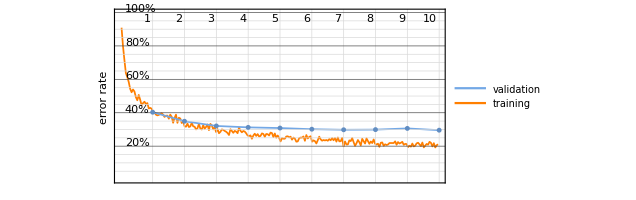

Ademxapp v1

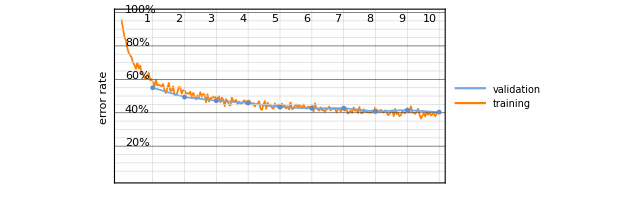

Inception v1

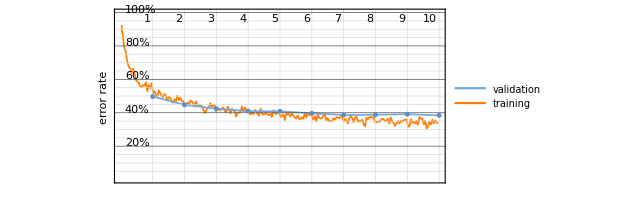

VGG-19 v1

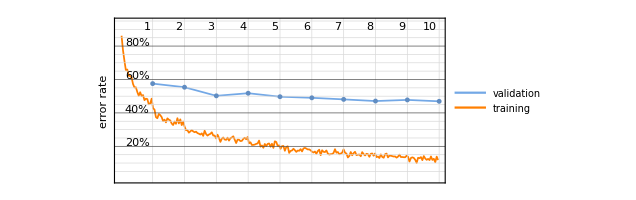

ResNet-152 v1

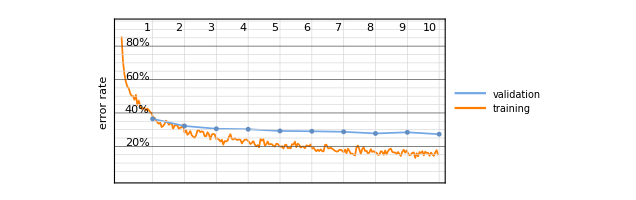

ImageIdentify v2

Ademxapp v2

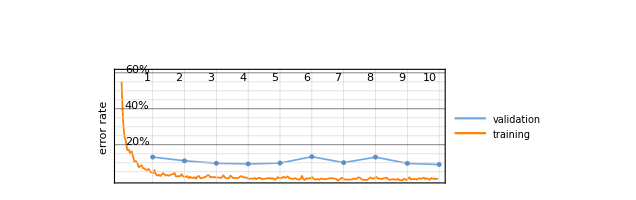

Inception v2

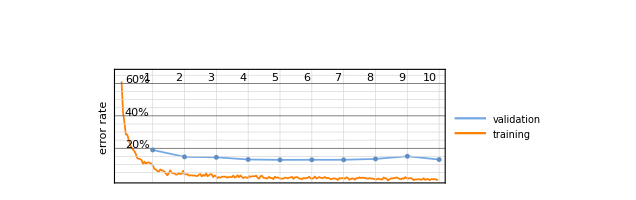

VGG-19 v2

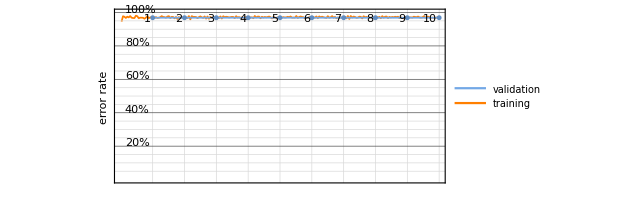

ResNet-152 v2

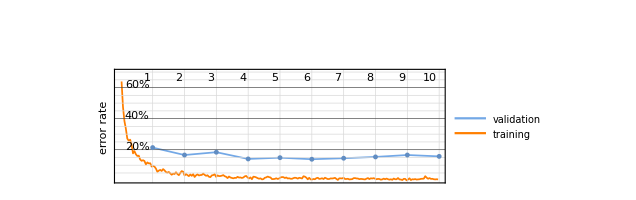

##### NetChains

ImageIdentify v1

```mathematica
NetChain[<>]
```

Ademxapp v1

```mathematica
NetChain[<>]
```

Inception v1

```mathematica
NetChain[<>]
```

VGG-19 v1

```mathematica
NetChain[<>]
```

ResNet-152 v1

```mathematica
NetChain[<>]
```

ImageIdentify v2

```mathematica
NetChain[<>]
```

Ademxapp v2

```mathematica
NetChain[<>]
```

Inception v2

```mathematica
NetChain[<>]
```

VGG-19 v2

```mathematica
NetChain[<>]
```

ResNet-152 v2

```mathematica
NetChain[<>]
```

##### Accuracy Comparison

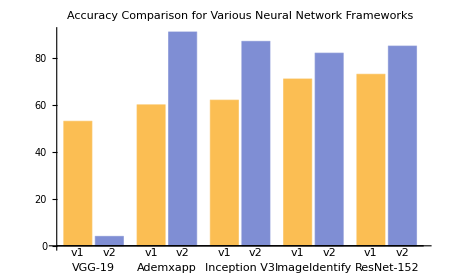

##### Speed Comparison

##### CloudDeploy

#### Data Sources Links/References

K.Simonyan, A.Zisserman, "Very Deep Convolutional Networks for Large-Scale Image Recognition," arXiv : 1409.1556 (2014)
(available from http : // www.robots.ox.ac.uk/~vgg/research/very_deep)
Rights : Creative Commons Attribution 4.0 International (CC BY 4.0)

K.He, X.Zhang, S.Ren, J.Sun, "Deep Residual Learning for Image Recognition," arXiv : 1512.03385 (2015)
(available from https : // github.com/KaimingHe/deep - residual - networks)
Rights : MIT License

C.Szegedy, V.Vanhoucke, S.Ioffe, J.Shlens, Z.Wojna, "Rethinking the Inception Architecture for Computer Vision," arXiv : 1512.00567 (2015)
(available from https : // github.com/tensorflow/models/blob/master/research/inception)
Rights : Apache 2.0 License

Z.Wu, C.Shen, A.van den Hengel, "Wider or Deeper: Revisiting the ResNet Model for Visual Recognition," arXiv : 1611.10080 (2016)
(available from https : // github.com/itijyou/ademxapp)
Rights : Apache 2.0 License

Wolfram Research (2018)
(available from http : // reference.wolfram.com/language/guide/SummaryOfNewFeaturesIn111.html)

Google Images

Yahoo Images

Amazon Inc.

Ebay Inc.

#### Future Directions

Use a more diverse dataset, recognize more categories of images.

Implement a faster version of the network/networks as an API for use as an app for mobile phones, part of a larger application that provides users with contextual awareness about their environment.

#### Keywords

Image Processing

Neural Networks

Transfer Learning

Image Analysis

CloudDeploy

Computer Science

Wolfram Language

PlugID